# Ring Calculations

## README

## Calculations

### Defining inputs:

!!! IMPORTANT !!!: Run the following cell first before any further calculation to define geometric parameters and  other inputs or constant.

```mathematica
<<Notation`;
Symbolize[Subscript[Ι, c]];
Symbolize[Subscript[Ω, c]];
Symbolize[Subscript[v, c]];
Symbolize[Subscript[U, c]];
Symbolize[Subscript[λ, 0]];
Symbolize[Subscript[ω, 0]];
```

```mathematica
(*setting physical contants*)
h = 6.62607004 * 10^-34; (*m^2 kg/s*)
c = 2.99792458*10^8; (*m/s^2*)
Subscript[k, B]=1.38064852*10^-23; (*J/K*)
Subscript[ϵ, 0]=8.854187*10^-12; (*C/Vm*)

(*modify the value below to set the inputs*)
R = 19.2* 10^-6; (*m; Radius of the ring*)
t = 0; (*m; width of the paddle*)
(*n = 1; qunatum number of the vertax*)
d=1; (*set to 2 if using dimers, 1 other wise*)
m  =d*23*1.660539*10^-27;(*kg; mass of the atoms; reference: Yb=173,^23 Na=23*)
Subscript[a, s] =2.75*10^-9; (*m; atomic s-wave scattering length; reference: Na=2.75nm, Li dimer=51.8nm*)
Ν= 6*10^5; (*normalization condition ((π g)/(m*Subscript[ω, ρ]*Subscript[ω, z]))(Subscript[μ, 0]/g)^2*2πR; total number of atoms *)
w= 10.5 * 10^-6; (*m; ODT light waist*)
Subscript[z, 0] = 2 * 10^-6; (*m; ODT light waist*)
(*referece values: Li^2 Subscript[S, 1/2](->)^2 Subscript[P, 3/2]: Subscript[λ, 0]=671nm, Γ/2π=6MHz; Yb^1 Subscript[S, 0](->)^1 Subscript[P, 1]: Subscript[λ, 0]=399nm,Γ/2π=29MHz,^1 Subscript[S, 0](->)^3 Subscript[P, 1]: Subscript[λ, 0]=556nm, Γ/2π=182kHz*)
Γ=2π*9.8*10^6; (*rad/s; Transition width, Na=9.8MHz, Li=5.87*10^6 Hz*)
Subscript[λ, 0]=589*10^-9; (*m; atom's wave length in vasuum, Na=589nm, Li=671nm *)
λ=1064*10^-9; (*m; laser wavelenght*)
Subscript[L, b]=0;

Subscript[P, ρ0]=1.3*10^-4; (*W*)
Subscript[P, z0]=0.5*10^-5;
```

### Polarizability

```mathematica
Subscript[ω, 0]=N[2π*c/Subscript[λ, 0]]; (*rad/s*)
ω=N[2π*c/λ]; (*rad/s*)
Subscript[Ι, sat]=(h Subscript[ω, 0]^3 Γ)/(2π*12π c^2); (*W/m^2=kg/s^3*)
α = N[d*((h Γ^2)/(2π*8))(1/(Subscript[ω, 0]-ω)+1/(Subscript[ω, 0]+ω))(1/Subscript[Ι, sat])](*m^2 s; polarizability*)
```

7.18943×10^-37

### The chemical potential of the ring

Definition: μ_0 = 1/π √ (Ngmω_ρ ω_z)/(2R) with N = ∫η(θ)R dθ = πg/(mω_ρ ω_z)(μ_0/g)^2 2πR

```mathematica
Subscript[Ι, ρ0]=(2 Subscript[P, ρ0])/(π w^2); (*W/m^2*)
Subscript[Ι, z0]=(2 Subscript[P, z0])/(π Subscript[z, 0]^2) ;
Subscript[U, ρ0]=α*Subscript[Ι, ρ0];(*J*)
Subscript[U, z0]=α*Subscript[Ι, z0];
Subscript[ω, ρ] =N[√((4 Subscript[U, ρ0])/(m w^2)) ]; (*rad/s; radial trap frequency*)
Subscript[ω, z] =N[ √((4 Subscript[U, z0])/(m Subscript[z, 0]^2))] ;(*vertical trap frequency*)
g = (4π Subscript[a, s](h/(2π))^2)/m; (*m^5 kg/s^2;strength of cintact interaction between atoms*)
Subscript[μ, 0] = 1/π √((Ν g m Subscript[ω, ρ] Subscript[ω, z])/(2R))(*J*)
```

1.29851×10^-30

### The critical barrier height and critical current

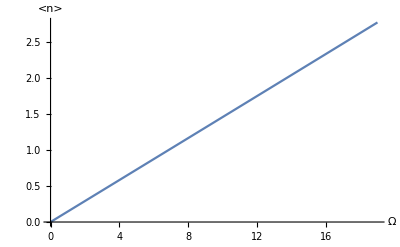

0.0263425 Ω

```mathematica
(*critical barrier and density profile at ρ=R, z=0*)
Subscript[κ, 0] = h/m; (*m^2/s*)
κ[Ω_]:=2π Ω R^2; (*m^2/s*)
l = 2π R - t ; (*m; length of the superfluid*)
η[n_]:=(π g)/(m Subscript[ω, ρ] Subscript[ω, z])n^2; (*kg/m!!!; 1D density*)
Subscript[n, ∞]=Subscript[μ, 0]/g; (*1/m^3*)
Subscript[v, c]=Subscript[Ω, c]*R; (*m/s*)
Subscript[n, b]= (Subscript[μ, 0]-0.5 Subscript[μ, 0])/g; (*1/m^3; density profile at the barrier*)
Subscript[L, R] = l/η[Subscript[n, ∞]]; (*m^2/kg*)
Subscript[Ι, c]=η[Subscript[n, b]] √((g Subscript[n, b])/(2m)); (*kg/s*)
Ι=η[Subscript[n, ∞]]*v;
v=Ω*R;
Subscript[Ω, c]=fre*2π;
Subscript[c, ∞]=√((g Subscript[n, ∞])/(2m)); (*m/s*)
Subscript[β, L]=2;

Plot[Subscript[μ, 0]/(1000*h)(1+1/4(Subscript[v, c]/Subscript[c, ∞])^2-5/4(Subscript[v, c]/Subscript[c, ∞])^(2/5)), {fre, 0, 35},FrameLabel->{"Ω_c/2π (Hz)", "U_c/h (kHz)"}, PlotStyle->{Red, Dashed}, Frame->True, PlotRangePadding->0];

Show[ContourPlot[0==κ[x*h/(2π m R^2)]/Subscript[κ, 0]+1/(2π)(Subscript[β, L] y+ArcSin[y]), {x, 0, 2},{y, -1,1}, FrameLabel->{"Ω/Ω_0", "I/I_c"}, PlotRangePadding->0],
ContourPlot[1==κ[x*h/(2π m R^2)]/Subscript[κ, 0]+1/(2π)(Subscript[β, L] y+ArcSin[y]), {x, 0, 2},{y, -1,1}, PlotRangePadding->0],
ContourPlot[2==κ[x*h/(2π m R^2)]/Subscript[κ, 0]+1/(2π)(Subscript[β, L] y+ArcSin[y]), {x, 0, 2},{y, -1,1}, PlotRangePadding->0]
];

y[x_,n_]:=Part[y /. NSolve[x==n-1/(2π)(Subscript[β, L] y+ArcSin[y]) && -1<y<1, y],1];
z[x_,n_]:=1/2 Subscript[β, L](y[x,n])^2+(1-Cos[2π x+Subscript[β, L] y[x,n]]);
ListPlot[{Table[{x,z[x,0]}, {x, 0, 0.56, 0.01}],Table[{x,z[x,1]}, {x, 0.432, 1.56, 0.01}],Table[{x,z[x,2]}, {x, 1.432, 2, 0.01}]}, AxesLabel->{"Ω/Ω_0","E/E_J"}];

Plot[κ[Ω]/Subscript[κ, 0]+1/(2π)(Subscript[β, L]*Ι/Subscript[Ι, c]+ArcSin[Ι/Subscript[Ι, c]]),{Ω,0,19},AxesLabel->{"Ω", "<n>"}];
```

```mathematica
I
```

```mathematica
Subscript[κ, 0] = h/m;
κ[Ω_]:=2π Ω R^2;
l = 2π R - t ; (*length of the superfluid*)
η[n_]:=(π g)/(m Subscript[ω, ρ] Subscript[ω, z])n^2; (*1D density*)
v=Ω*R;
Subscript[n, ∞]=Subscript[μ, 0]/g;
Subscript[n, b]=(Subscript[μ, 0]-0.5 Subscript[μ, 0])/g;(* density profile at the barrier*)
η[Subscript[n, b]];
Subscript[L, R] = l/η[Subscript[n, ∞]];
Subscript[Ι, c]=η[Subscript[n, b]] √((g Subscript[n, b])/(2m))
Ι=η[Subscript[n, ∞]]*v;
γ[Ι_]:=ArcSin[Ι/Subscript[Ι, c]]+2π ((Subscript[L, b]*Ι)/Subscript[κ, 0]); (*phase difference across the juction*)
Solve[1/(2π)(2π κ[Ω]/Subscript[κ, 0]+2π (Subscript[L, R] Subscript[Ι, c])/Subscript[κ, 0]+γ[Subscript[Ι, c]])==1,Ω];
Ω=2π*3;

1/(2π)(2π (2π *3*2π* R^2)/Subscript[κ, 0]+2π (Subscript[L, R] Ι)/Subscript[κ, 0]+γ[Ι])
Subscript[L, J]=Subscript[κ, 0]/(2π Subscript[Ι, c]);
Subscript[L, R]/Subscript[L, J];
```